```mathematica
(* This is to get the SSM potential between Ca and Cl*)
```

```mathematica
(* The main task is to get v_{R1,Ca Water} , v_{R1, Cl Water} and  v_{R1,Ca Cl}. I will denote it by fvR1CaA, fvR1ClA and fvR1CaCl respectively *)
```

```mathematica
(* This handling of the surface charge is a bit tricky. Maybe use a smoothed charge will make the analysis easier. I can just use the delta charge for now *)
(* when a surface charge of Q is convoluted with a potention ϕ. The 
 result is NIntegrate[Q/2 ϕ[Sqrt[rqcut^2+r^2-2 r rqcut x]],{x,-1,1}], where rqcut is the position of the surface charge *)
```

```mathematica
(* The screening charge around ion Ca is denoted by frhoqCa for the full system and frhoqCa0 for the GT system. Definition is similar for the Cl *)
```

```mathematica
Quit[]
```

```mathematica
ϵ=71
```

71

```mathematica
Qca=2
Qcashield=-Qca (1 -1/ϵ)
```

2

-140/71

```mathematica
Qcl=-1
Qclshield=-Qcl(1 -1/ϵ)
```

-1

70/71

```mathematica
d=0.2
ss=6
fintqcorrect[r_]:=Piecewise[{{0, r<d}, {Erf[(r-d)/ss], r≥d}}]
frhoqcorrect[r_]:=Piecewise[{{0, r<d}, {fintqcorrect'[r]/(4π r^2), r≥d}}]
```

0.2

6

```mathematica
frhoqcorrect2[r_]:=Piecewise[{{0, r<d}, {(Erf'[(r-d)/ss]/ss)/(4π r^2), r≥d}}]
```

```mathematica
frhoqcorrect[0.21]
```

0.339355

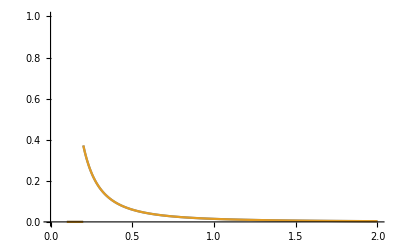

```mathematica
Plot[{frhoqcorrect[r],frhoqcorrect2[r]},{r,0.1,2},PlotRange->{0,1}]
```

```mathematica
NIntegrate[frhoqcorrect2[r]4π r^2,{r,0,100}]
```

1.

```mathematica
(* frhoqCa0=frhoqCa-Qcashield frhoqcorrect, without considering the surface charge, total surface charge is Qcashield-Qcacut *)
```

```mathematica
rrhoqCa=Import["/Users/anggao/Desktop/Na_Ca_Cl_potentials/rhoq_Ca_full.txt","Table"];
```

```mathematica
frhoqCa=Interpolation[rrhoqCa]
```

InterpolatingFunction[{{0.001,1.999}},<>]

```mathematica
rrhoqCl=Import["/Users/anggao/Desktop/Na_Ca_Cl_potentials/rhoq_Cl_full.txt","Table"];
```

```mathematica
frhoqCl=Interpolation[rrhoqCl]
```

InterpolatingFunction[{{0.001,1.999}},<>]

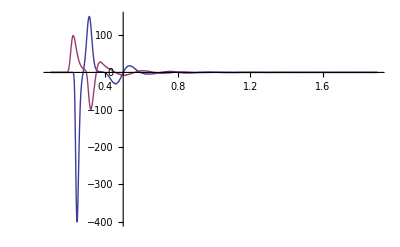

```mathematica
Plot[{frhoqCa[r],frhoqCl[r]},{r,0.1,1.9},PlotRange->Full]
```

```mathematica
frhoqCa0[r_]:=frhoqCa[r]-Qcashield frhoqcorrect[r]
```

```mathematica
frhoqCl0[r_]:=frhoqCl[r]-Qclshield frhoqcorrect[r]
```

```mathematica
rqcut=1.99
```

1.99

```mathematica
Qcacut=NIntegrate[frhoqCa[rp] 4 π rp^2,{rp,0,rqcut}]
```

-1.99988

```mathematica
Qcacut-Qcashield
```

-0.0280509

```mathematica
Qclcut=NIntegrate[frhoqCl[rp] 4 π rp^2,{rp,0,rqcut}]
```

0.962526

```mathematica
Qclcut-Qclshield
```

-0.0233893

```mathematica
fG[r_,rp_,s_]:=1/(2 r rp)(Abs[r+rp] Erf[Abs[r+rp]/s] + s/Sqrt[π] Exp[-(Abs[r+rp]/s)^2] 
            - Abs[r-rp]Erf[Abs[r-rp]/s] - s/Sqrt[π] Exp[-(Abs[r-rp]/s)^2] )
```

```mathematica
rhosurf[r_,rcut_]:=DiracDelta[r-rcut]/(4 π rcut^2)
```

```mathematica
fVR1surf[r_,rcut_]:=1/(2 r rcut)(-0.28209479177387814 ⅇ^(-4. Abs[r-rcut]^2)+0.28209479177387814 ⅇ^(-4. Abs[r+rcut]^2)-Abs[r-rcut] Erf[2. Abs[r-rcut]]+Abs[r+rcut] Erf[2. Abs[r+rcut]])
```

```mathematica
(* to get fVR1surf, we already assumed that the smoothed length sigma=0.5 *)
```

```mathematica
(* Calculate fVR1CaA first *)
```

```mathematica
s=0.5 (* the sigma parameter for v1 *)
```

0.5

```mathematica
frenormCaA[r_?NumericQ]:=NIntegrate[frhoqCa[rp]fG[r,rp,s]4π rp^2,{rp,0.01,rqcut}]+(Qcashield-Qcacut) fVR1surf[r,rqcut]
```

```mathematica
tableVrenormCaA=ParallelTable[frenormCaA[r],{r,0.01,4.91,0.05}]
```

{-4.29763,-4.27907,-4.2346,-4.16566,-4.07445,-3.96375,-3.83681,-3.69711,-3.54822,-3.39361,-3.23649,-3.07974,-2.92579,-2.77661,-2.63369,-2.4981,-2.37047,-2.25111,-2.14004,-2.03706,-1.94181,-1.85385,-1.77266,-1.6977,-1.62843,-1.56434,-1.50494,-1.44979,-1.39847,-1.35062,-1.30592,-1.26406,-1.2248,-1.1879,-1.15316,-1.12039,-1.08943,-1.06014,-1.03238,-1.00604,-0.981009,-0.957195,-0.93451,-0.912877,-0.892223,-0.872484,-0.853599,-0.835515,-0.818182,-0.801553,-0.785587,-0.770244,-0.755489,-0.741288,-0.727612,-0.714431,-0.701719,-0.689451,-0.677605,-0.666159,-0.655093,-0.644389,-0.634029,-0.623997,-0.614278,-0.604856,-0.595719,-0.586854,-0.57825,-0.569893,-0.561775,-0.553885,-0.546214,-0.538752,-0.531491,-0.524423,-0.517541,-0.510837,-0.504305,-0.497937,-0.491728,-0.485673,-0.479764,-0.473998,-0.468368,-0.462871,-0.457501,-0.452255,-0.447127,-0.442115,-0.437213,-0.432419,-0.427729,-0.42314,-0.418648,-0.41425,-0.409944,-0.405727,-0.401595}

```mathematica
interpVrenormCaA=Interpolation[Transpose[{Table[r,{r,0.01,4.91,0.05}],tableVrenormCaA}]]
```

InterpolatingFunction[{{0.01,4.91}},<>]

```mathematica
fVR1CaA[r_]:=Piecewise[{{interpVrenormCaA[r]+Qca Erf[r/s]/r, r<4.5}, {Qca/(ϵ r), r≥ 4.5}}]
```

```mathematica
fvR1CaA[r_]:=fVR1CaA[r]/Qca
```

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

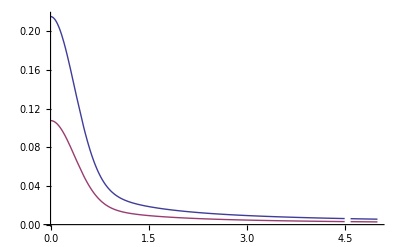

```mathematica
Plot[{fVR1CaA[r],fvR1CaA[r]},{r,0,5},PlotRange->Full]
```

```mathematica
(* successfully obtained fvR1CaA *)
```

```mathematica
fvR1CaA[0.5]
```

0.0514134

```mathematica
frenormClA[r_?NumericQ]:=NIntegrate[frhoqCl[rp]fG[r,rp,s]4π rp^2,{rp,0.01,rqcut}]+(Qclshield-Qclcut) fVR1surf[r,rqcut]
```

```mathematica
tableVrenormClA=ParallelTable[frenormClA[r],{r,0.01,4.91,0.05}]
```

{2.16426,2.15475,2.13198,2.0967,2.05005,1.99349,1.92869,1.85748,1.78168,1.70309,1.62334,1.54392,1.46603,1.39068,1.3186,1.25032,1.18613,1.12616,1.07042,1.01878,0.97105,0.926994,0.886344,0.848825,0.814161,0.782093,0.752376,0.724785,0.699116,0.675187,0.652832,0.631905,0.612277,0.593833,0.576468,0.560091,0.544621,0.529984,0.516115,0.502954,0.490448,0.47855,0.467215,0.456406,0.446085,0.436221,0.426783,0.417744,0.409081,0.400769,0.392787,0.385117,0.377741,0.370642,0.363804,0.357214,0.350859,0.344725,0.338802,0.333079,0.327546,0.322194,0.317015,0.311999,0.307139,0.302428,0.29786,0.293427,0.289125,0.284947,0.280888,0.276943,0.273107,0.269376,0.265745,0.262212,0.25877,0.255419,0.252152,0.248969,0.245864,0.242836,0.239882,0.236999,0.234184,0.231436,0.228751,0.226127,0.223564,0.221057,0.218607,0.21621,0.213865,0.21157,0.209324,0.207125,0.204972,0.202863,0.200797}

```mathematica
interpVrenormClA=Interpolation[Transpose[{Table[r,{r,0.01,4.91,0.05}],tableVrenormClA}]]
```

InterpolatingFunction[{{0.01,4.91}},<>]

```mathematica
fVR1ClA[r_]:=Piecewise[{{interpVrenormClA[r]+Qcl Erf[r/s]/r, r<4.5}, {Qcl/(ϵ r), r≥ 4.5}}]
```

```mathematica
fvR1ClA[r_]:=fVR1ClA[r]/Qcl
```

InterpolatingFunction::dmval: Input value {0.0000921329} lies outside the range of data in the interpolating function. Extrapolation will be used.

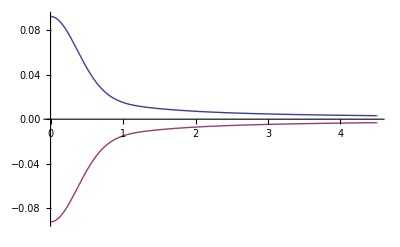

```mathematica
Plot[{fvR1ClA[r],fVR1ClA[r]},{r,0,4.51},PlotRange->Full]
```

```mathematica
frenormCaCl[r_?NumericQ]:=-1/Qca(NIntegrate[2 π rp^2 frhoqCa[rp] (fvR1ClA[Sqrt[rp^2+r^2-2 r rp x]]-Erf[Sqrt[rp^2+r^2-2 r rp x]/s]/Sqrt[rp^2+r^2-2 r rp x]),{rp, 0.01, rqcut},{x,-1,1}]+ NIntegrate[(Qcashield-Qcacut)/2 (fvR1ClA[Sqrt[rqcut^2+r^2-2 r rqcut x]]-Erf[Sqrt[rqcut^2+r^2-2 r rqcut x]/s]/Sqrt[rqcut^2+r^2-2 r rqcut x]),{x,-1,1}])
```

```mathematica
tablerenormCaCl=ParallelTable[frenormCaCl[r],{r,0.005,3,0.05}]
```

{-2.06523,-2.05797,-2.03883,-2.00841,-1.96763,-1.91767,-1.85995,-1.79599,-1.72737,-1.65567,-1.58234,-1.50873,-1.43599,-1.36508,-1.29675,-1.23157,-1.1699,-1.11195,-1.05779,-1.00739,-0.960611,-0.917293,-0.877215,-0.840146,-0.805844,-0.774072,-0.744607,-0.717235,-0.691762,-0.668011,-0.645822,-0.625052,-0.605573,-0.58727,-0.570042,-0.553796,-0.538453,-0.523938,-0.510187,-0.49714,-0.484746,-0.472955,-0.461726,-0.451017,-0.440795,-0.431025,-0.42168,-0.412731,-0.404154,-0.395926,-0.388025,-0.380434,-0.373134,-0.366108,-0.359342,-0.352821,-0.346533,-0.340464,-0.334605,-0.328943}

```mathematica
interprenormCaCl=Interpolation[Transpose[{Table[r,{r,0.005,3,0.05}],tablerenormCaCl}]]
```

InterpolatingFunction[{{0.005,2.955}},<>]

```mathematica
fvR1CaCl[r_]:=Piecewise[{{interprenormCaCl[r]+Erf[r/s]/r, r<2.9}, {2/(ϵ r)-1/(ϵ^2 r), r≥2.9}}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

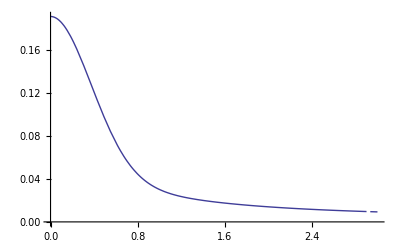

```mathematica
Plot[fvR1CaCl[r],{r,0,3}]
```

```mathematica
(*now calculate vtildeR1CaCl, I will use fvtR1CaCl to denote it.*)
```

```mathematica
fomegaCaCl[r_]:=NIntegrate[2 π rp^2(frhoqCa[rp])Qcl fvR1ClA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01, rqcut},{x,-1,1}]+
1/2 NIntegrate[2 π rp^2(-Qcashield frhoqcorrect[rp])Qcl fvR1ClA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01, 20},{x,-1,1}]+
NIntegrate[(Qcashield-Qcacut)/2 Qcl fvR1ClA[Sqrt[rqcut^2+r^2-2 r rqcut x]],{x,-1,1}]+NIntegrate[2 π rp^2(frhoqCl[rp])Qca fvR1CaA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01, rqcut},{x,-1,1}]+
1/2 NIntegrate[2 π rp^2(-Qclshield frhoqcorrect[rp])Qca fvR1CaA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01,20},{x,-1,1}]+
NIntegrate[(Qclshield-Qclcut)/2 Qca fvR1CaA[Sqrt[rqcut^2+r^2-2 r rqcut x]],{x,-1,1}]
```

```mathematica
tableomegaCaCl=ParallelTable[fomegaCaCl[r],{r,0.005,4,0.05}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.119775 and 3.57544×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0279513 and 7.11022×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0543597 and 5.13196×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.137366 and 5.51972×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0275651 and 7.81681×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0574576 and 7.88332×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.108873 and 4.39753×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0262623 and 4.44874×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0483615 and 7.94071×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.174793 and 1.95355×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.140464 and 2.05696×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.163415 and 3.0277×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0201208 and 2.19416×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.019333 and 5.59871×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0194452 and 3.30349×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0162086 and 1.81357×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0134825 and 9.5258×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0115034 and 4.23518×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0154104 and 3.07907×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0128503 and 1.56777×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0110337 and 6.7559×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0157629 and 1.63112×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0131597 and 7.05916×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0112681 and 3.86078×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.010046 and 2.14837×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00966505 and 3.53699×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00986897 and 1.9512×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00907221 and 1.30161×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00873228 and 5.372×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00731806 and 2.78312×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00796289 and 1.16728×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00892832 and 1.20946×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00784764 and 1.05755×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00773568 and 1.04863×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

{0.345104,0.341964,0.33376,0.320911,0.304061,0.284024,0.261717,0.238073,0.214005,0.190331,0.167732,0.14673,0.127682,0.110785,0.0960927,0.0835439,0.0729916,0.0642334,0.0570369,0.051163,0.0463824,0.0424859,0.0392921,0.0366486,0.0344307,0.0325409,0.0309032,0.0294604,0.0281692,0.0269986,0.0259254,0.0249327,0.024008,0.0231421,0.0223282,0.0215607,0.0208353,0.0201486,0.0194978,0.0188804,0.0182939,0.017737,0.0172076,0.0167044,0.0162257,0.0157704,0.0153369,0.0149243,0.0145311,0.0141564,0.013799,0.0134579,0.0131321,0.0128206,0.0125226,0.0122372,0.0119637,0.0117013,0.0114495,0.0112075,0.0109748,0.0107509,0.0105353,0.0103276,0.0101274,0.00993427,0.00974787,0.00956789,0.00939402,0.00922597,0.00906348,0.00890629,0.00875417,0.00860688,0.00846424,0.00832602,0.00819205,0.00806214,0.00793612,0.00781384}

```mathematica
interpomegaCaCl=Interpolation[Transpose[{Table[r,{r,0.005,4,0.05}],tableomegaCaCl}]]
```

InterpolatingFunction[{{0.005,3.955}},<>]

```mathematica
fvtR1CaCl[r_]:=Piecewise[{{interpomegaCaCl[r]/(Qca Qcl)+fvR1CaCl[r], r<3.9}, {1/(ϵ r), r>=3.9}}]
```

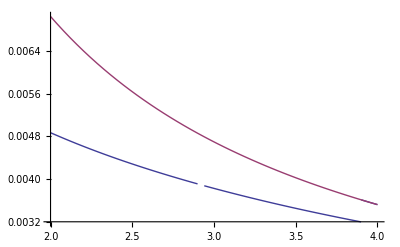

```mathematica
Plot[{fvtR1CaCl[r],1/(ϵ r)},{r,2,4},PlotRange->Full]
```

```mathematica
tableomegaCaCllong=ParallelTable[fomegaCaCl[r],{r,0.005,10,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.061308 and 1.15451×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0216747 and 3.95577×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0145443 and 1.27148×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.065671 and 8.08175×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0138324 and 3.42301×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0209422 and 6.35626×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0543597 and 5.13196×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0141741 and 1.13269×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0208587 and 3.41739×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.174793 and 1.95355×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.140464 and 2.05696×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.163415 and 3.0277×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0108269 and 3.26765×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0104035 and 5.25276×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0106198 and 2.77248×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0086539 and 9.97015×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00832989 and 1.58881×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00852294 and 9.32567×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{0.345104,0.341964,0.33376,0.320911,0.304061,0.284024,0.261717,0.238073,0.214005,0.190331,0.167732,0.14673,0.127682,0.110785,0.0960927,0.0835439,0.0729916,0.0642334,0.0570369,0.051163,0.0463824,0.0424859,0.0392921,0.0366486,0.0344307,0.0325409,0.0309032,0.0294604,0.0281692,0.0269986,0.0259254,0.0249327,0.024008,0.0231421,0.0223282,0.0215607,0.0208353,0.0201486,0.0194978,0.0188804,0.0182939,0.017737,0.0172076,0.0167044,0.0162257,0.0157704,0.0153369,0.0149243,0.0145311,0.0141564,0.013799,0.0134579,0.0131321,0.0128206,0.0125226,0.0122372,0.0119637,0.0117013,0.0114495,0.0112075,0.0109748,0.0107509,0.0105353,0.0103276,0.0101274,0.00993427,0.00974787,0.00956789,0.00939402,0.00922597,0.00906348,0.00890629,0.00875417,0.00860688,0.00846424,0.00832602,0.00819205,0.00806214,0.00793612,0.00781384,0.00769514,0.00757989,0.00746793,0.00735915,0.00725341,0.00715061,0.00705062,0.00695334,0.00685868,0.00676653,0.0066768,0.00658941,0.00650426,0.00642128,0.0063404,0.00626153,0.00618462,0.00610958,0.00603636,0.0059649,0.00589513,0.00582701,0.00576047,0.00569546,0.00563194,0.00556986,0.00550916,0.00544982,0.00539177,0.005335,0.00527944,0.00522507,0.00517186,0.00511976,0.00506874,0.00501877,0.00496983,0.00492187,0.00487487,0.00482881,0.00478365,0.00473937,0.00469595,0.00465336,0.00461158,0.00457058,0.00453035,0.00449086,0.0044521,0.00441404,0.00437666,0.00433995,0.00430389,0.00426846,0.00423365,0.00419944,0.00416582,0.00413276,0.00410026,0.0040683,0.00403687,0.00400595,0.00397554,0.00394562,0.00391617,0.00388719,0.00385867,0.00383059,0.00380294,0.00377572,0.00374891,0.00372251,0.0036965,0.00367088,0.00364563,0.00362076,0.00359624,0.00357208,0.00354826,0.00352478,0.00350163,0.0034788,0.00345629,0.00343408,0.00341218,0.00339057,0.00336926,0.00334823,0.00332747,0.00330699,0.00328677,0.00326682,0.00324712,0.00322767,0.00320847,0.0031895,0.00317078,0.00315228,0.00313402,0.00311597,0.00309815,0.00308053,0.00306313,0.00304594,0.00302894,0.00301215,0.00299555,0.00297914,0.00296292,0.00294688,0.00293103,0.00291535,0.00289985,0.00288452,0.00286936,0.00285436,0.00283953,0.00282486,0.00281034,0.00279598}

```mathematica
interpomegaCaCllong=Interpolation[Transpose[{Table[r,{r,0.005,10,0.05}],tableomegaCaCllong}]]
```

InterpolatingFunction[{{0.005,9.955}},<>]

```mathematica
fvtR1CaCllong[r_]:=Piecewise[{{interpomegaCaCllong[r]/(Qca Qcl)+fvR1CaCl[r], r<9.9}, {1/(ϵ r), r≥9.9}}]
```

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

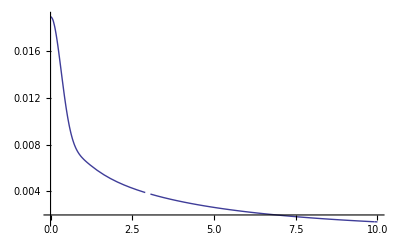

```mathematica
Plot[{fvtR1CaCllong[r]},{r,0,10},PlotRange->Full]
```

```mathematica
Export["/Users/anggao/Desktop/Na_Ca_Cl_potentials/vR1_CaCl.txt", Transpose[{Table[r,{r,0.02,20,0.02}], Table[fvtR1CaCllong[r],{r,0.02,20,0.02}]}], "Table"]
```

/Users/anggao/Desktop/Na_Ca_Cl_potentials/vR1_CaCl.txt

```mathematica
fvtR1CaCllong[0.2]
```

0.016873

```mathematica
box=2.97
```

2.97

```mathematica
fvtR1CaCllongs[r_]:=fvtR1CaCllong[r]-Erf[r/10]/(ϵ r)
```

```mathematica
fEwaldCaCl[x_]:=Sum[Qca Qcl fvtR1CaCllongs[Sqrt[(m box-x)^2+(l box)^2+(n box)^2]],{m,-20,20},{l,-20,20},{n,-20,20}]
```

```mathematica
tableEwaldCaCl=ParallelTable[fEwaldCaCl[r],{r,0.1,1.5,0.05}]
```

{-0.320773,-0.319492,-0.317873,-0.315923,-0.313805,-0.31164,-0.309531,-0.307557,-0.305778,-0.304256,-0.302949,-0.301877,-0.301018,-0.300318,-0.299796,-0.299394,-0.299084,-0.298842,-0.298628,-0.298469,-0.298335,-0.298222,-0.298126,-0.298046,-0.297981,-0.297957,-0.297923,-0.297956,-0.297952}

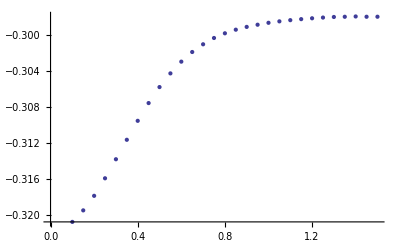

```mathematica
ListPlot[Transpose[{Table[r,{r,0.1,1.5,0.05}], tableEwaldCaCl}]]
```

```mathematica
interpEwaldCaCl=Interpolation[Transpose[{Table[r,{r,0.1,1.5,0.05}], tableEwaldCaCl}]]
```

InterpolatingFunction[{{0.1,1.5}},<>]

```mathematica
Export["/Users/anggao/Desktop/Na_Ca_Cl_potentials/VR1CaCl_Ewald.txt",Transpose[{Table[r,{r,0.1,box/2,0.001}], Table[interpEwaldCaCl[r]-interpEwaldCaCl[box/2],{r,0.1,box/2,0.001}]}],"Table"]
```

/Users/anggao/Desktop/Na_Ca_Cl_potentials/VR1CaCl_Ewald.txt

```mathematica
140*(interpEwaldCaCl[0.3]-interpEwaldCaCl[box/2])
```

-2.21782